relevant equations. 1/gamma decay time, D diffusion coefficient, q wavevector, k_B Boltzmann constant, T the temperature, eta solvent viscosity, R particle radius
gamma = 2 D q^2 ; D = k_B T/6 Pi eta R (=diffcoef)

This line is just to clear the memory

```mathematica
Remove["Global`*"]
```

all results go in res array

```mathematica
res={};
```

Function to perform cumulant fit with a, b, gamma, and d fit parameters, 1/gamma the decay time, t the time, and d the first cumulant

```mathematica
gi[a_,b_,gamma_,d_,t_]=a+b Exp[-gamma t+d t^2]
```

a+b ⅇ^(-gamma t+d t^2)

output file - only needs to be defined once.

```mathematica
output="C:\\Users\\aarts\\Dropbox\\dphils\\adam\\MOF DLS\\A100_M.dat"; (*To be adjusted by user*)
```

input file - needs to be changed for each angle; after the first angle, start from here.

```mathematica
dataall=Import["C:\\Users\\aarts\\Dropbox\\dphils\\adam\\MOF DLS\\A100_M-150.ASC","Table"]; (*To be adjusted by user*)
```

Solvent and system parameters go here; n refractive index, lambda wavelength, temperature (temp) and angle are read from the file; theta is the angl in radians

```mathematica
n=1.332; (*To be adjusted by user*)
lambda=632.8 10^-9; (*To be adjusted by user*)
postemp=Position[dataall,"Temperature"][[1,1]];
temp=dataall[[postemp,4]]
posangle=Position[dataall,"Angle"][[1,1]];
angle=dataall[[posangle,4]]
theta=angle Pi/180;
q=4Pi n/lambda Sin[theta/2]
kT=1.3806488 10^-23 temp
eta=0.00089; (*To be adjusted by user*)
```

301.246

150.

2.555×10^7

4.15915×10^-21

extract the right data from the file - you may want to change the Take from datafit

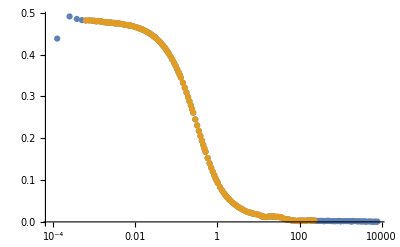

```mathematica
posav=Position[dataall,"Average"][[1,1]];
poscountrate=Position[dataall,"Count Rate"][[1,1]];
data=dataall[[posav+1;;poscountrate-2,{1,2}]];
datafit=Take[data,{5,150}]; (*To be adjusted by user*)
ListLogLinearPlot[{data,datafit}]
```

actual fitting with a cumulant fit

{a→0.0191198,b→0.453851,gamma→2.23222,d→0.00953837}

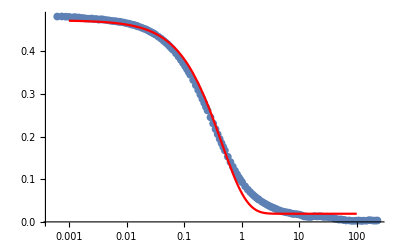

1.70972×10^-12

1.45007×10^-7

```mathematica
out=FindFit[datafit,gi[a,b,gamma,d,t],{{a,0.25},{b,0.25},{gamma,0.01},{d,0.0001}},t]
Show[{ListLogLinearPlot[datafit],LogLinearPlot[gi[a,b,gamma,d,t]/.out,{t,0.001,100},PlotRange->All,PlotStyle->Red]}]
difcoeff=(gamma/.out)/(2 q^2 10^-3)
radius=kT/(6 Pi eta difcoeff)
```

creating an output array

```mathematica
AppendTo[res,{angle, q^2,gamma/.out, radius}]
```

{{30.,4.68692×10^13,0.0897577,2.58923×10^-7},{60.,1.74918×10^14,0.49519,1.75155×10^-7},{90.,3.49837×10^14,1.1772,1.4735×10^-7},{120.,5.24755×10^14,2.11419,1.23068×10^-7},{150.,6.52804×10^14,2.23222,1.45007×10^-7}}

Exporting the output array - only to be done at the very end; after all angles! Plot to do is gamma vs q^2 of which the slope whould be 2D

```mathematica
Export[output,Sort@res,"Data"]
```

C:\Users\aarts\Dropbox\dphils\adam\MOF DLS\A100_M.dat